```mathematica
f[x_,h_,r_]:=h+x*r-x^2
```

```mathematica
p1=ContourPlot3D[f[x,y,z]==0,{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[h+r*x - x^2 ,{x,-10,10}],{r,-20,20},{h,-10,10}]
```

If two FP exsist then left one is unstabel and right one is stable. Becouse f.b4(x*) >0 on left and f.b4(x*) <0 on right

Solve::bddom: Value r of the domain argument should be Complexes, Reals, Algebraics, Rationals, Integers, Primes, or Automatic.

```mathematica
f[x_]=h+r*x-x^2
fps=Solve[f[x]==0,x]//Flatten//Simplify
```

h+r x-x^2

{x→1/2 (r-√(4 h+r^2)),x→1/2 (r+√(4 h+r^2))}

```mathematica
D[f[x],x] //Flatten//Simplify
D[f[x],x]/.fps[[2]] //Flatten//Simplify
```

r-2 x

-√(4 h+r^2)

```mathematica
xMax=Solve[D[f[x],x] ==0]
```

```mathematica
{{x->r/2}}
```

```mathematica
f[xMax]//Flatten //Simplify
```

{h+r (x→r/2)-(x→r/2)^2}

```mathematica
-(r*r/2-r^2/4)//Simplify
```

-r^2/4

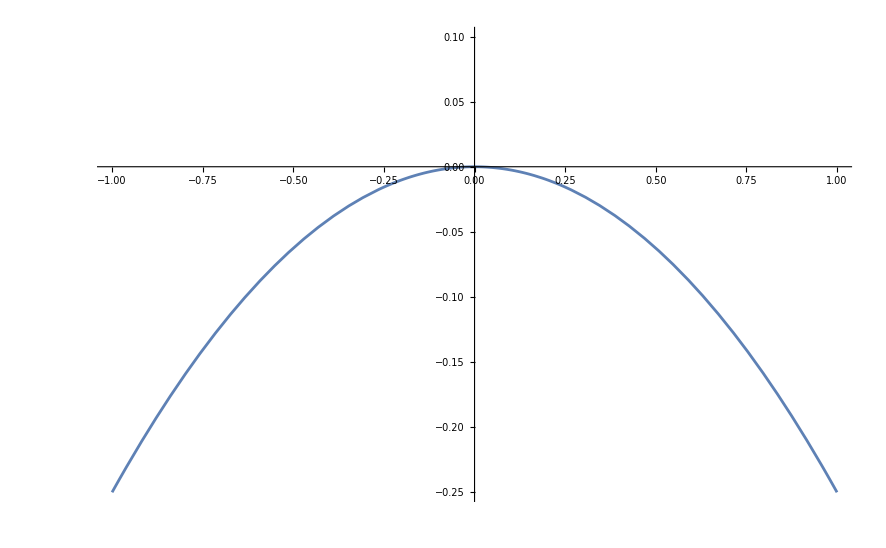

```mathematica
p2=Plot[-(r^2/4),{r,-1,1},PlotRange->{{-1,1},{-0.25,0.1}}]
```